```mathematica
Copyright © 2021 Franz Utermohlen. All rights reserved.
```

```mathematica
Clear["Global`*"];
a=t=1;
a1=a/2{3,Sqrt[3]};
a2=a/2{3,-Sqrt[3]};
δ1=a/2{1,Sqrt[3]};
δ2=a/2{1,-Sqrt[3]};
δ3=-a{1,0};
Kpoint={2π/(3a),2π/(3Sqrt[3]a)};
Δ[kx_,ky_]:=Exp[I{kx,ky}.δ1]+Exp[I{kx,ky}.δ2]+Exp[I{kx,ky}.δ3];
(*h[kx_,ky_]:=-t({{0, Δ[kx,ky]}, {Conjugate[Δ[kx,ky]], 0}});*)
(*Ep and Em are the energy eigenvalues*)
energyband[kx_,ky_]:=t Abs[Δ[kx,ky]];
(*energyband[kx_,ky_]:=t Sqrt[Conjugate[Δ[kx,ky]]Δ[kx,ky]];*)
energybandgapped[kx_,ky_,m_]:=t Sqrt[Abs[Δ[kx,ky]]^2+m^2];
(*f=4 cos((3 a kx)/2) cos(1/2 √3 a ky)+2 cos(√3 a ky);*)

(*Plots*)
functions={energyband[kx,ky],-energyband[kx,ky]};
xmin=-π;
xmax=π;
ymin=xmin;
ymax=xmax;
xlabel="k_xa";
ylabel="k_ya";
zlabel="E(k) /"HoldForm[Abs[t]];
xticks=Table[i,{i,xmin,xmax,π/2}];
yticks=xticks;
zticks=Automatic;
ticks={xticks,yticks,zticks};
plotsize=500;
plotsettings={AxesLabel->{xlabel,ylabel,zlabel},LabelStyle->Directive[16,Black],Ticks->ticks,ImageSize->plotsize};
Plot3D[functions,{kx,xmin,xmax},{ky,ymin,ymax},Evaluate[plotsettings]]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

-Graphics3D- -Graphics3D-

```mathematica
(*Plot of a Dirac cone*)
functions1={energyband[qx+Kpoint[[1]],qy+Kpoint[[2]]],-energyband[qx+Kpoint[[1]],qy+Kpoint[[2]]]};
smallq=π/100;
xmin=-smallq;
xmax=smallq;
ymin=-smallq;
ymax=smallq;
xlabel="q_xa";
ylabel="q_ya";
zlabel="E(q→0)"/HoldForm[Abs[t]];
(*xticks={-smallq,0,smallq};
yticks={-smallq,0,smallq};
zticks=Automatic;*)
xticks={0};
yticks={0};
zticks={0};
ticks={xticks,yticks,zticks};
plotsize=500;
plotsettings={AxesLabel->{xlabel,ylabel,zlabel},LabelStyle->Directive[16,Black],Ticks->ticks,PlotRange->{-3/2smallq,3/2smallq},ClippingStyle->None,ImageSize->plotsize};
Plot3D[functions1,{qx,xmin,xmax},{qy,ymin,ymax},Evaluate[plotsettings]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Plot of Dirac cone with added "mass term"*)
m=t/100;
functions2={energybandgapped[qx+Kpoint[[1]],qy+Kpoint[[2]],m],-energybandgapped[qx+Kpoint[[1]],qy+Kpoint[[2]],m]};
smallq=π/100;
xmin=-smallq;
xmax=smallq;
ymin=-smallq;
ymax=smallq;
xlabel="q_xa";
ylabel="q_ya";
zlabel="E(q→0)"/HoldForm[Abs[t]];
(*xticks={-smallq,0,smallq};
yticks={-smallq,0,smallq};
zticks=Automatic;*)
xticks={0};
yticks={0};
zticks={0};
ticks={xticks,yticks,zticks};
plotsize=500;
plotsettings={AxesLabel->{xlabel,ylabel,zlabel},LabelStyle->Directive[16,Black],Ticks->ticks,PlotRange->{-3/2smallq,3/2smallq},ClippingStyle->None,ImageSize->plotsize};
Plot3D[functions2,{qx,xmin,xmax},{qy,ymin,ymax},Evaluate[plotsettings]]
```

-Graphics3D-

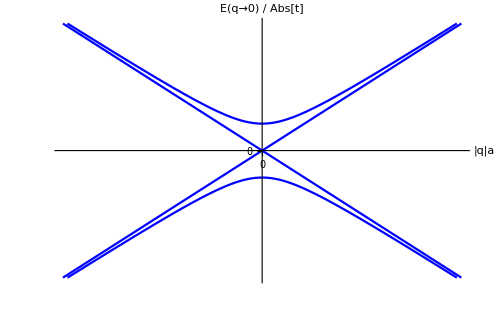

```mathematica
(*2D plot of Dirac cone with and without gap*)
m=t/100;
functions1={energyband[qx+Kpoint[[1]],qy+Kpoint[[2]]],-energyband[qx+Kpoint[[1]],qy+Kpoint[[2]]]};
functions2={energybandgapped[qx+Kpoint[[1]],qy+Kpoint[[2]],m],-energybandgapped[qx+Kpoint[[1]],qy+Kpoint[[2]],m]};
smallq=π/100;
xmin=-smallq;
xmax=smallq;
ymin=-smallq;
ymax=smallq;
xlabel="|q|a";
ylabel="E(q→0) /"HoldForm[Abs[t]];
xticks={0};
yticks={0};
zticks={0};
ticks={xticks,yticks,zticks};
plotsize=500;
plotsettings={AxesLabel->{xlabel,ylabel,zlabel},LabelStyle->Directive[16,Black],Ticks->ticks,PlotRange->{-3/2smallq,3/2smallq},ClippingStyle->None,ImageSize->plotsize,PlotStyle->Blue};
Plot[{functions1,functions2}/.qy->0,{qx,xmin,xmax},Evaluate[plotsettings]]
```

```mathematica
(*Expand Ep about a Dirac point DP (i.e., about small q)*)
(*Choose the Dirac point*)
DP=Kpoint;
q=ϵ{qx,qy};
k=q+DP;
kx=k[[1]];
ky=k[[2]];
hDirac=(*SeriesCoefficient[*)
FullSimplify[
energyband[kx,ky]/.qy->0
,Assumptions->{a>0,qx∈Reals,qy∈Reals,ϵ∈Reals}]
(*,{ϵ,0}]*)
```

2 Abs[sin((3 qx ϵ)/4)]